### Definitions

```mathematica
Np =4;
d = 2;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3, x4}
xpcoord = {x1p,x2p,x3p, x4p}
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
```

-1<k&&Im[k]==0

{x1,x2,x3,x4}

{x1p,x2p,x3p,x4p}

### Coefficients from Analytical Calculation

```mathematica
p0101int[ax_,bx_,ay_,by_]:=
12*(√((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-4 ax bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)+bx^2 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)) π^4)/(64 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4 ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))))
```

```mathematica
p0000int[ax_,bx_,ay_,by_]:=12*(√((ax (ax-2 bx))/(ax-bx)) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^2 (2 ay^2-8 ay by+7 by^2)-4 ax bx (2 ay^2-8 ay by+7 by^2)+bx^2 (7 ay^2-28 ay by+24 by^2)) π^4)/(16 ax^4 ay^4 (ax-3 bx)^2 (ax-bx)^(3/2) (ay-3 by)^2 (ay-by)^(3/2) ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))));
```

```mathematica
p1010int[ax_,bx_,ay_,by_]:=12*(bx^2 (ax^4 (2 ay^2-8 ay by+7 by^2)-8 ax^3 bx (2 ay^2-8 ay by+7 by^2)-12 ax bx^3 (5 ay^2-20 ay by+18 by^2)+6 bx^4 (7 ay^2-28 ay by+24 by^2)+ax^2 bx^2 (47 ay^2-188 ay by+166 by^2)) π^4)/(64 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √(ay-by) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) (ay^2-4 ay by+3 by^2) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))));

p1010int[ax_,bx_,ay_,by_]:=12*(bx^2 (ax^4 (2 ay^2-8 ay by+7 by^2)-8 ax^3 bx (2 ay^2-8 ay by+7 by^2)-12 ax bx^3 (5 ay^2-20 ay by+18 by^2)+6 bx^4 (7 ay^2-28 ay by+24 by^2)+ax^2 bx^2 (47 ay^2-188 ay by+166 by^2)) π^4)/(64 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) √((ay (ay-2 by))/(ay-by)) √(ay-by) √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) (ay^2-4 ay by+3 by^2) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))));
```

```mathematica
p1111int[ax_,bx_, ay_, by_]:=12*(bx^2 √((ay (ay-2 by))/(ay-by)) √(ay-by) by^2 √((2 ay^2-5 ay by+by^2)/(ay-2 by)) √((ay (ay^2-3 ay by+by^2))/(2 ay^2-5 ay by+by^2)) √((ay (ay^2-4 ay by+3 by^2))/(2 ay^2-7 ay by+4 by^2)) √((ay (2 ay^2-7 ay by+4 by^2))/(ay^2-3 ay by+by^2)) (ax^4 (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-8 ax^3 bx (2 ay^4-16 ay^3 by+47 ay^2 by^2-60 ay by^3+42 by^4)-12 ax bx^3 (5 ay^4-40 ay^3 by+116 ay^2 by^2-144 ay by^3+108 by^4)+6 bx^4 (7 ay^4-56 ay^3 by+166 ay^2 by^2-216 ay by^3+144 by^4)+ax^2 bx^2 (47 ay^4-376 ay^3 by+1100 ay^2 by^2-1392 ay by^3+996 by^4)) π^4)/(256 ay^4 √((ax (ax-2 bx))/(ax-bx)) √(ax-bx) √((2 ax^2-5 ax bx+bx^2)/(ax-2 bx)) √((ax (ax^2-3 ax bx+bx^2))/(2 ax^2-5 ax bx+bx^2)) (ax^2-4 ax bx+3 bx^2)^3 √((ax (ax^2-4 ax bx+3 bx^2))/(2 ax^2-7 ax bx+4 bx^2)) √((ax (2 ax^2-7 ax bx+4 bx^2))/(ax^2-3 ax bx+bx^2)) (ay^2-4 ay by+3 by^2)^4 ((3 π^4)/(8 √(ax^5 ay^5 (ax-4 bx) (ay-4 by)))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax (ay-by))/ay^7))-(ay^(5/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(11 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(11 (ay/ax)^(5/2) bx by π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay (ax-3 bx) √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx √((ay (ay-by))/ax) by π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(9 bx by^2 π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))-(3 bx by^2 π^(7/2))/(2 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-((ax-3 bx) √(ay (ay-by)) by^2 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 (ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √((ay (ay-by))/ax) by^2 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √((ay (ay-by))/(ax^5 (ax-4 bx)^3 (ay-4 by)^3)) by^2 π^(7/2))/(16 √2 (ay-2 by)^2)-(ay^(5/2) bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(15 ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+(ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay bx √(ay-by) by^3 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(5 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(9 bx (ay-by) by^3 π^(7/2))/(8 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(69 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(13 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(17 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(15 (ax-3 bx) by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-((ax-3 bx) by^4 π^(7/2))/(8 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(bx √(ay-by) by^4 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(7 bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 (ax-3 bx) by^4 π^(7/2))/(4 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))-(129 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(45 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(ay^2 (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) (ay-by)^2 by^4 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(8 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 bx by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(5 bx by^5 π^(7/2))/(√2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(5 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(5 bx by^5 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(16 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))-(15 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(√2 (ax-3 bx) (ay-by) by^5 π^(7/2))/(ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(5 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(8 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))+(3 (ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(bx by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))-(17 bx by^6 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+((ax-3 bx) (ay-by) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-((ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(11 (ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+(5 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 ay bx by^2 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))+(63 bx by^3 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax-(ax by)/ay))-(7 (ax-3 bx) by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2)+(7 bx by √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2)+(ay bx by^2 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(32 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2)+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(17 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 (ax-3 bx) by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx by^7 π^(7/2))/(2 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(49 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(5 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(5 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 (ax-3 bx) by^4 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(39 bx by^4 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(19 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(3 ay bx by^2 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay^2 (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(5 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(7 bx by^3 π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^(5/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 (ax-3 bx) by^3 π^(7/2))/(8 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 bx by^3 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(5 (ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(71 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(17 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(11 bx by^5 π^(7/2))/(4 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(9 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(9 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by)))))+1/(ay-by)^(5/2)2 √(2 π) ((ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^9))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^5 (ay-by))))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(ay^(7/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(13 bx by π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^7))+(3 bx by π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(9 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by))/(ay^3 (ay-by))))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(9 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(bx by^2 π^(7/2))/(4 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))-(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by))/(ay (ay-by))))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^2 π^(7/2))/(16 √2 ax^2 (((ax-4 bx) (ay-4 by))/ay)^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^2 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(3 ay^(5/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(ay^3 (ax-3 bx) (ay-by) by^2 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax ay)/(ay-by)))+(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(5 bx by^3 π^(7/2))/(16 √2 ax ay (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))-(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay (ay-by))/ax) by^3 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(((ax-2 bx) (ay-by))/ay))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(5 bx by^3 π^(7/2))/(8 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(7 ay^2 (ax-3 bx) (ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(9 ay^3 (ax-3 bx) (ay-by) by^3 π^(7/2))/(32 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-2 by) (ay-by)) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^(5/2))+(5 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))+(9 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-(bx by^4 π^(7/2))/(4 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax ay)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+(37 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))+(119 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax ay (ay-4 by))/(ay-by)))-(45 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+((ax-3 bx) √(ay-by) by^4 π^(7/2))/(8 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(ay (ax-3 bx) √(ay-by) by^4 π^(7/2))/(16 √2 ax (ax ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √(ay-by) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(5 (ax-3 bx) √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √((ay-by)/ax) by^4 π^(7/2))/(16 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(13 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(13 ay (ax-3 bx) (ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(7 √ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(29 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(11 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+(3 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-((ax-3 bx) √((ay-by)/ax) by^5 π^(7/2))/(8 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx √((ay-by)/ax) by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(3 bx by^5 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax (ay-by)))-(25 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(19 bx by^5 π^(7/2))/(8 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) √((ay-4 by) (ay-by)) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)-(117 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(2 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(37 (ax-3 bx) by^5 π^(7/2))/(2 √2 (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax^2 ay (ay-4 by) (ay-by)))+(3 (ax-3 bx) (ay-by) by^5 π^(7/2))/(8 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(7 ay (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(47 bx by^5 π^(7/2))/(2 √2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(9 ay bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))-((ax-3 bx) by^6 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(7 bx by^6 π^(7/2))/(4 √2 ax^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax (ay-by)))+(bx by^6 π^(7/2))/(4 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ax ay (ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(5 √2 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(13 bx by^6 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay^3 (ax-4 bx)^3 (ay-4 by) (ay-by)))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(2 √2 ax^2 ay^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax ay (ay-by)))+(3 bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(2 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(ay (ax-3 bx) by^2 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-((ax-3 bx) by^3 π^(7/2))/(4 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(3 bx by^3 π^(7/2))/(8 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(ay bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(19 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+((ax-3 bx) by^4 π^(7/2))/(ax (ax (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(25 bx by^4 π^(7/2))/(16 √2 ax^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ax-(ax by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ay^2-ay by)))+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 √(ay^2-5 ay by+4 by^2) π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by)^2 (ay-3 by) (ay-2 by)^2)+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(3 ay (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(27 ay (ax-3 bx) by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(39 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(71 ay^2 bx by^2 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(211 ay bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(ay bx by^3 π^(7/2))/(2 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(23 bx by^4 π^(7/2))/(√2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(7 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8/ay+6/(-ay+by)))+(39 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-(5 (ax-3 bx) by π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(bx by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(ay^2 (ax-3 bx) by π^(7/2))/(16 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(51 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))+(15 bx by^3 π^(7/2))/(8 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (8/ay+6/(-ay+by))))-(11 bx (ay/(ax^2-6 ax bx+8 bx^2))^(3/2) (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 (ax-3 bx) by^3 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(5 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^4 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(97 (ax-3 bx) by^5 π^(7/2))/(32 ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(11 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) (ax-3 bx) π^(7/2))/(32 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-((ay/(ax-4 bx))^(3/2) bx π^(7/2))/(16 ax^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+(17 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(32 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(5 (ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^2 (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))+1/(ay-by)^(5/2)2 √(2 π) ((ay^(7/2) (ax-3 bx) π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(ay^(7/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-((ay/ax)^(5/2) bx π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))-(3 (ay/ax)^(5/2) (ax-3 bx) by π^(7/2))/(8 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(ay^(5/2) bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(3 ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(3 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ay-2 by)^2 √((ay-4 by) (ay-by)))+(ay^(7/2) bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(3 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))-(bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))+((ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx) (ay-2 by)^2 √((ax ay (ax-4 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ay/ax)^(5/2) (ax-3 bx) by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-((ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))-(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay (ay-by)) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) (ay/((ax-4 bx) (ay-4 by)))^(3/2) by^2 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(15 ay^2 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(83 (ay/ax)^(5/2) bx by^2 π^(7/2))/(16 √2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(bx (ay-by) by^2 π^(7/2))/(4 √2 ax (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(ay^(5/2) (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(32 √2 ax^3 ((ax-4 bx) (ax-3 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax-3 bx) (ax-2 bx) (ay-4 by) (ay-by)))+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay/(ay-by)))+(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ay (ax-2 bx))/(ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay (ay-by))))+(3 bx by^3 π^(7/2))/(16 √2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))-(ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(ay (ax-3 bx) √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(3 ay bx √(ay-by) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 ay bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(69 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(135 (ay/(ax-4 bx))^(3/2) (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(49 bx by^3 π^(7/2))/(16 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ax (ay-4 by) (ay-by))/ay^3))-(3 (ax-3 bx) by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(3 bx by^3 π^(7/2))/(4 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(bx (ay-by) by^3 π^(7/2))/(16 √2 ax ay (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(8 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))-(5 ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^3 π^(7/2))/(16 √2 ax^3 (ax-4 bx) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))/ay))+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay/(ay-by)))-(7 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))+(23 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ax^2-6 ax bx+8 bx^2)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay (ay-4 by))/(ay-by)))-(59 (ax-3 bx) by^4 π^(7/2))/(32 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(59 bx by^4 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay (ax-4 bx)^3 (ay-4 by))/(ay-by)))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(16 √2 ax^3 ay^(5/2) (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))-(13 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ay (ax-2 bx) (ay-4 by))/(ay-by)))+(bx by^4 π^(7/2))/(8 √2 (ay-3 by) √((ax^5 ay (ax-4 bx)^3 (ay-4 by)^3 (ay-2 by)^4)/(ay-by)))+((ax-3 bx) by^4 π^(7/2))/(32 √2 ax (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(ay (ax-3 bx) by^4 π^(7/2))/(16 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))-(7 (ax-3 bx) √(ay-by) by^4 π^(7/2))/(32 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^4 π^(7/2))/(16 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(11 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)+(2 √2 (ax-3 bx) by^4 π^(7/2))/(ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(13 bx by^4 π^(7/2))/(16 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ay-by)))+(45 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))+(ay (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(25 bx (ay-by) by^4 π^(7/2))/(16 √2 ax ay (ay-3 by) (ay-2 by)^2 ((ax (ax-4 bx) (ay-4 by) (ay-by))/ay)^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(39 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^4 π^(7/2))/(32 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by) (ay-by))/ay))+(167 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx)/(ay-by)))-(55 bx by^5 π^(7/2))/(16 √2 (ay-3 by)^2 (ay-2 by)^2 √((ax^5 ay^3 (ax-4 bx)^3 (ay-4 by))/(ay-by)))+(27 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(((ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^5 π^(7/2))/(4 √2 ax (ay-3 by) (ay-2 by)^2 ((ax ay (ax-4 bx) (ay-4 by))/(ay-by))^(3/2) (ay-by))+(5 (ax-3 bx) √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(bx √(ay-by) by^5 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2)+(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-2 by)^2)-(bx √(ay-by) by^5 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(3 bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay (ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)-(81 (ax-3 bx) by^5 π^(7/2))/(32 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))+(7 bx by^5 π^(7/2))/(2 √2 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ay-by)))-(15 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax-2 bx) (ay-by)))-(5 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(32 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay (ax-2 bx) (ay-by)))-(413 (ax-3 bx) by^5 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(9 (ax-3 bx) (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^5 π^(7/2))/(4 √2 ax^(5/2) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(37 bx by^5 π^(7/2))/(√2 (ay-3 by)^2 (ay-2 by)^2 √(ax^5 ay (ax-4 bx)^3 (ay-4 by) (ay-by)))-(37 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^5 π^(7/2))/(16 √2 ax^3 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(27 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(13 ay bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^5 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(9 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(16 √2 ax^2 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax^2 ay (ax-2 bx) (ay-4 by))/(ay-by)))+((ax-3 bx) by^6 π^(7/2))/(2 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))+(bx by^6 π^(7/2))/(4 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(ay-by))-(5 (ax-3 bx) √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(7 bx √(ay-by) by^6 π^(7/2))/(16 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+(bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) √(ay-by) by^6 π^(7/2))/(8 √2 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax^2-6 ax bx+8 bx^2) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2)+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax-2 bx) (ay-by)))+(23 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((ay-4 by) (ay-by)))-(13 ax bx by^6 π^(7/2))/(√2 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-4 by) (ay-by)))+(29 (ax-3 bx) by^6 π^(7/2))/(8 √2 ax^(5/2) ay (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))+(√2 (ax-3 bx) (ay-by) by^6 π^(7/2))/(ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))-(3 bx (ay-by) by^6 π^(7/2))/(√2 ax^(5/2) (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ay-4 by) (ay-by))^(3/2))+(17 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^(7/2))/(8 √2 ax^3 (ay (ax-4 bx))^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √((ax-2 bx) (ay-4 by) (ay-by)))+(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))+(3 bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) (ay-by) by^6 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(5 (ax-3 bx) by^7 π^(7/2))/(8 √2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(bx by^7 π^(7/2))/(√2 (ax ay)^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(ay-by))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^7 π^(7/2))/(2 √2 ax^3 ay^2 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay-4 by) (ay-by)))-(3 (√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^(7/2))/(4 √2 ax^3 ay^2 (ax-4 bx)^(3/2) (ax-3 bx)^2 (ay-3 by)^2 (ay-2 by)^2 √(ay (ax-2 bx) (ay-4 by) (ay-by)))+(bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) (ay-by) by^7 π^(7/2))/(4 √2 ax^3 ay (ax-3 bx)^2 (ay-3 by) (ay-2 by)^2 (ay (ax-4 bx) (ax-2 bx) (ay-4 by) (ay-by))^(3/2))-(7 bx by^5 π^(7/2))/(4 (ax^2 ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √((2 ay-8 by)/(ax ay-ax by)))-(ay (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(47 ay bx by^2 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(57 (ax-3 bx) by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^3 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √(2-(2 by)/ay))-(9 ay (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))+(51 (ax-3 bx) by^4 π^(7/2))/(32 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-(7 bx by^4 π^(7/2))/(16 ax^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √(2-(2 by)/ay))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^2 π^(7/2))/(16 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((2 ax-4 bx)/(ay^2-ay by)))+(9 (ax-3 bx) by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(16 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2)+(ay^(9/2) (ax-3 bx) π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(ay^(9/2) bx π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(13 ay^(7/2) (ax-3 bx) by π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(7 ay^(7/2) bx by π^(7/2))/(8 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(11 ay^(5/2) bx (√(ax^7 (ax-2 bx))-8 √(ax^5 (ax-2 bx)) bx+21 √(ax^3 (ax-2 bx)) bx^2-18 √(ax (ax-2 bx)) bx^3) by^2 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+((ax-3 bx) by^4 π^(7/2))/(8 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(bx by^4 π^(7/2))/(4 √2 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(23 (ax-3 bx) by^6 π^(7/2))/(2 √2 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(5 √2 bx by^6 π^(7/2))/(ax (ax ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))-(15 (ax-3 bx) by^7 π^(7/2))/(4 √2 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(3 √2 bx by^7 π^(7/2))/((ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay^2-5 ay by+4 by^2))+(71 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^5 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay (ay^2-5 ay by+4 by^2)))-(9 bx by^3 √((ay^2-ay by)/(2 ay-8 by)) π^(7/2))/(8 ax (ax (ax-4 bx))^(3/2) (ay^2-5 ay by+6 by^2)^2)+(3 ay bx by π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(13 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(13 bx by^2 π^(7/2))/(16 √2 ax (ax (ax-4 bx))^(3/2) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(11 ay (ax-3 bx) by^2 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(ay bx by^2 π^(7/2))/(4 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(33 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^3 π^(7/2))/(4 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(81 ay (ax-3 bx) by^3 π^(7/2))/(16 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(135 ay bx by^3 π^(7/2))/(8 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay bx by^3 π^(7/2))/(2 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(775 (ax-3 bx) by^4 π^(7/2))/(32 √2 ax^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(65 bx by^4 π^(7/2))/(2 √2 ax (ax (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(113 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(16 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))-(3 bx (-√(ax^7 (ax-2 bx))+8 √(ax^5 (ax-2 bx)) bx-21 √(ax^3 (ax-2 bx)) bx^2+18 √(ax (ax-2 bx)) bx^3) by^4 π^(7/2))/(8 √2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ay-5 by+(4 by^2)/ay))+(ay^2 (ax-3 bx) π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(33 ay (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(143 ay^2 (ax-3 bx) by^2 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))-(7 ay (ax-3 bx) by^3 π^(7/2))/(32 √2 ax^2 (ax-4 bx)^(3/2) (ay-4 by) (ay-3 by) (ay-2 by)^2 √(ax (ay-5 by+(4 by^2)/ay)))+(bx (√(ax^7 (ax-2 bx))+bx (-8 √(ax^5 (ax-2 bx))+3 bx (7 √(ax^3 (ax-2 bx))-6 √(ax (ax-2 bx)) bx))) by^3 π^(7/2))/(2 ax^3 (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8/ay+6/(-ay+by)))-((ay/(ax-4 bx))^(3/2) (ax-3 bx) by^2 π^(7/2))/(16 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(8 ax^(5/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(3 (ax-3 bx) by^3 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx by^3 π^(7/2))/(16 ax (ax ay (ax-4 bx))^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+((ax-3 bx) by^4 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(bx by^4 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(83 (ax-3 bx) by^5 π^(7/2))/(32 ax^(5/2) (ay (ax-4 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(7 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^5 π^(7/2))/(4 ax^3 (ax-3 bx)^2 (ay (ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-(21 (ax-3 bx) by^6 π^(7/2))/(16 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(21 bx by^6 π^(7/2))/(8 (ax ay)^(5/2) (ax-4 bx)^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))+(3 bx (-√(ax^7 (ax-2 bx))+bx (8 √(ax^5 (ax-2 bx))+3 bx (-7 √(ax^3 (ax-2 bx))+6 √(ax (ax-2 bx)) bx))) by^6 π^(7/2))/(4 ax^3 ay^(5/2) (ax-3 bx)^2 ((ax-4 bx) (ax-2 bx))^(3/2) (ay-3 by)^2 (ay-2 by)^2 √(8+(6 ay)/(-ay+by)))-((ay/(ax-4 bx))^(3/2) bx by^2 π^(7/2))/(16 ax^2 (ay-3 by)^2 (ay-2 by)^2 √(ax (8+(6 ay)/(-ay+by))))+((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^6 π^3)/(√2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π)))-((√(ax^7 (ax-2 bx))-9 bx (√(ax^5 (ax-2 bx))+3 √(ax (ax-2 bx)) bx (-ax+bx))) by^7 π^3)/(8 √2 ax^2 (ay (ax-3 bx))^(5/2) ((ax-4 bx) (ay-4 by))^(3/2) (ay-3 by) (ay-2 by)^2 √((ax^2 (ax-2 bx) (ay-by))/(ax π-3 bx π))))));
```

```mathematica
p00upi[ax_, bx_, ay_, by_]:=(4 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p01upi[ax_, bx_, ay_, by_]:=(12 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) by^2)/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p10upi[ax_, bx_, ay_, by_]:=(12 √ax √ay bx^2 √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p11upi[ax_, bx_, ay_, by_]:=(36 √ax √ay bx^2 √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) by^2)/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p20upi[ax_, bx_, ay_, by_]:=(4 √ax √ay bx^2 (2 ax^2-8 ax bx+17 bx^2) √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2)^2 √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p02upi[ax_,bx_, ay_, by_]:= (4 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) by^2 (2 ay^2-8 ay by+17 by^2))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2)^2 √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
```

```mathematica
p00di[ax_,bx_, ay_, by_]:=(4 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) (8 ax^2 (2 ay^2-8 ay by+5 by^2)-32 ax bx (2 ay^2-8 ay by+5 by^2)+bx^2 (40 ay^2-160 ay by+91 by^2)))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p01di[ax_,bx_, ay_, by_]:=(4 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) (8 ax^2 (8 ay^4-64 ay^3 by+152 ay^2 by^2-96 ay by^3+31 by^4)-32 ax bx (8 ay^4-64 ay^3 by+152 ay^2 by^2-96 ay by^3+31 by^4)+bx^2 (112 ay^4-896 ay^3 by+2164 ay^2 by^2-1488 ay by^3+497 by^4)))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2)^2 √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p10di[ax_,bx_, ay_, by_]:=(4 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) (16 ax^4 (4 ay^2-16 ay by+7 by^2)-128 ax^3 bx (4 ay^2-16 ay by+7 by^2)-48 ax bx^3 (16 ay^2-64 ay by+31 by^2)+bx^4 (248 ay^2-992 ay by+497 by^2)+4 ax^2 bx^2 (304 ay^2-1216 ay by+541 by^2)))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2)^2 √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p11di[ax_,bx_, ay_, by_]:=(12 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) (16 ax^4 by^2 (4 ay^2-16 ay by+7 by^2)-128 ax^3 bx by^2 (4 ay^2-16 ay by+7 by^2)-16 ax bx^3 (16 ay^4-128 ay^3 by+340 ay^2 by^2-336 ay by^3+125 by^4)+4 ax^2 bx^2 (16 ay^4-128 ay^3 by+596 ay^2 by^2-1360 ay by^3+573 by^4)+bx^4 (112 ay^4-896 ay^3 by+2292 ay^2 by^2-2000 ay by^3+721 by^4)))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2)^2 √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2)^2 √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p20di[ax_,bx_, ay_, by_]:= (12 √ax √ay bx^2 √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) (16 ax^4 (6 ay^2-24 ay by+11 by^2)-128 ax^3 bx (6 ay^2-24 ay by+11 by^2)-8 ax bx^3 (96 ay^2-384 ay by+209 by^2)+6 ax^2 bx^2 (288 ay^2-1152 ay by+539 by^2)+bx^4 (312 ay^2-1248 ay by+665 by^2)))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2)^3 √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2) √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
p02di[ax_,bx_, ay_, by_]:=(12 √ax √ay √((ax ay (ax-4 bx) (ay-4 by))/((ax-3 bx) (ay-3 by))) by^2 (24 ax^2 (4 ay^4-32 ay^3 by+72 ay^2 by^2-32 ay by^3+13 by^4)-96 ax bx (4 ay^4-32 ay^3 by+72 ay^2 by^2-32 ay by^3+13 by^4)+bx^2 (176 ay^4-1408 ay^3 by+3234 ay^2 by^2-1672 ay by^3+665 by^4)))/(√((4 ax^2-14 ax bx+3 bx^2)/(ax-3 bx)) (4 ax^2-16 ax bx+7 bx^2) √((ax (4 ax^2-16 ax bx+7 bx^2))/(4 ax^2-14 ax bx+3 bx^2)) √((4 ay^2-14 ay by+3 by^2)/(ay-3 by)) (4 ay^2-16 ay by+7 by^2)^3 √((ay (4 ay^2-16 ay by+7 by^2))/(4 ay^2-14 ay by+3 by^2)))
```

```mathematica
p0up[kx_, ky_]:=p00upi[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p0000int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p1up[kx_, ky_]:=p10upi[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p1010int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p2up[kx_, ky_]:=p01upi[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p0101int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p3up[kx_, ky_]:=p11upi[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p1111int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
(*p4up[k_]:=p4upi[A[lp[k]], B[1,lp[k],3]]-p44int[A[lp[k]], B[1,lp[k],3]]
p5up[k_]:=p5upi[A[lp[k]], B[1,lp[k],3]]-p55int[A[lp[k]], B[1,lp[k],3]]
p6up[k_]:=p6upi[A[lp[k]], B[1,lp[k],3]]-p66int[A[lp[k]], B[1,lp[k],3]]
p7up[k_]:=p7upi[A[lp[k]], B[1,lp[k],3]]-p77int[A[lp[k]], B[1,lp[k],3]]
p8up[k_]:=p8upi[A[lp[k]], B[1,lp[k],3]]-p88int[A[lp[k]], B[1,lp[k],3]]*)
```

```mathematica
p1111int[1,5,1,5]
```

(3073014375 π^4)/(986911342592 ((516881041 π^4)/13938365952-1/8 ⅈ √(π/2) ((882662699 ⅈ π^(7/2))/(1742295744 √2)+(8750 ⅈ √2 π^(7/2))/555579)-1/8 ⅈ √(π/2) ((34580617 ⅈ π^(7/2))/(217786968 √2)-(21875 ⅈ √2 π^(7/2))/555579)))

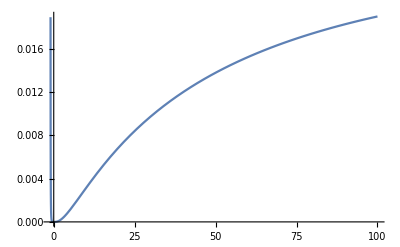

```mathematica
Plot[p3up[k, k], {k,-0.99,100}]
```

```mathematica
p0d[kx_, ky_]:=p00di[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p0000int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p1d[kx_, ky_]:=p10di[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p1010int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p2d[kx_, ky_]:=p01di[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p0101int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p3d[kx_, ky_]:=p11di[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]-p1111int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
(*p4down[k_]:=p4downi[A[lp[k]], B[1,lp[k],3]]-p44int[A[lp[k]], B[1,lp[k],3]]
p5down[k_]:=p5downi[A[lp[k]], B[1,lp[k],3]]-p55int[A[lp[k]], B[1,lp[k],3]]
p6down[k_]:=p6downi[A[lp[k]], B[1,lp[k],3]]-p66int[A[lp[k]], B[1,lp[k],3]]
p7down[k_]:=p7downi[A[lp[k]], B[1,lp[k],3]]-p77int[A[lp[k]], B[1,lp[k],3]]
p8down[k_]:=p8downi[A[lp[k]], B[1,lp[k],3]]-p88int[A[lp[k]], B[1,lp[k],3]]*)
```

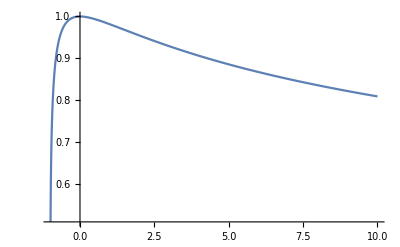

```mathematica
Plot[p1d[k, k], {k,-0.99,10}]
```

```mathematica
p0updown[kx_, ky_]:= p0000int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p1updown[kx_, ky_]:= p1010int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p2updown[kx_, ky_]:= p0101int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]
p3updown[kx_, ky_]:= p1111int[A[lp[kx]], B[1,lp[kx],Np], A[lp[ky]], B[1,lp[ky],Np]]

p3updown[10,15]
(*p4updown[k_]:= p44int[A[lp[k]], B[1,lp[k],3]]
p5updown[k_]:= p55int[A[lp[k]], B[1,lp[k],3]]
p6updown[k_]:= p66int[A[lp[k]], B[1,lp[k],3]]
p7updown[k_]:= p77int[A[lp[k]], B[1,lp[k],3]]
p8updown[k_]:= p88int[A[lp[k]], B[1,lp[k],3]]*)

p0vac[kx_, ky_]:= 1-p0up[kx, ky]-p0d[kx, ky]-p0updown[kx, ky]
p1vac[kx_, ky_]:= 1-p1up[kx, ky]-p1d[kx, ky]-p1updown[kx, ky]
p2vac[kx_, ky_]:= 1-p2up[kx, ky]-p2d[kx, ky]-p2updown[kx, ky]
p3vac[kx_, ky_]:= 1-p3up[kx, ky]-p3d[kx, ky]-p3updown[kx, ky]
(*p4vac[k_]:= 1-p4up[k]-p4down[k]-p4updown[k]
p5vac[k_]:= 1-p5up[k]-p5down[k]-p5updown[k]
p6vac[k_]:= 1-p6up[k]-p6down[k]-p6updown[k]
p7vac[k_]:= 1-p7up[k]-p7down[k]-p7updown[k]
p8vac[k_]:= 1-p8up[k]-p8down[k]-p8updown[k]*)
```

(622854144 (-1+1/(√11))^2 (10117/1015021568-(10117 (-1+1/(√11)))/(46137344 √11)+(118409 (-1+1/(√11))^2)/738197504-(37473 (-1+1/(√11))^3)/(67108864 √11)+(13395 (-1+1/(√11))^4)/134217728) π^4)/(753571 √91 (1/44-(-1+1/(√11))/(4 √11)+3/64 (-1+1/(√11))^2)^(7/2) (4224 11^(1/4) √(2/(1/(2 √11)+1/2 (1-1/(√11)))) π^4+16384/49 √(π/7) (-(1617 √(7/2) 11^(1/4) (-1+1/(√11)) π^(7/2))/(512 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(3916 √(2/7) 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(4225 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(263351 √(7/2) 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(25600 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(445600199 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(4326400 √14 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2)))+16384/49 √(π/7) (-(473 √(2/7) 11^(1/4) (-1+1/(√11)) π^(7/2))/(4225 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))-(406439 √(7/2) 11^(1/4) (-1+1/(√11)) π^(7/2))/(34611200 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))-(12120471 11^(1/4) (-1+1/(√11)) π^(7/2))/(1384448 √14 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(51876 √(2/7) 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(4225 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(3615491 √(7/2) 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(865280 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(272325141 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(4326400 √14 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(66 11^(1/4) √14 (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(4225 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(1089 √(11/7) (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))-((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))-(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(8450 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(891 √77 (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))-((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))-(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(25600 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))-(36531 √(11/7) (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(108160 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(5015043 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(34611200 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(5247 √(11/7) (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(3200 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))+(16112943 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(34611200 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))+(3896849 √(11/(7 (1/(2 √11)+1/4 (1-1/(√11))))) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^(7/2))/(166400 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(216887 √(77/(1/(2 √11)+1/4 (1-1/(√11)))) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^(7/2))/(41600 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(99 √(77/(2 (1/(√11)+1/2 (1-1/(√11))))) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^(7/2))/(1600 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(11711931 √77 (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) (-(√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) ((7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))-(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(17305600 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(25628053 √(11/7) (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) ((√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) (-(7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))+(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(17305600 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(1198989 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) ((√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) (-(7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))+(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(2163200 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(1089 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) ((√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) (-(7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))+(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(33800 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))+(8019 ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^3 √((11 (π/(2 √11)-3/8 (-1+1/(√11)) π))/(7 (1/(2 √11)+1/4 (1-1/(√11))))))/(41600 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^(5/2)))+16384/49 √(π/7) (-(44 √(2/7) 11^(1/4) (-1+1/(√11)) π^(7/2))/(4225 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(6970887 √(7/2) 11^(1/4) (-1+1/(√11)) π^(7/2))/(34611200 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))-(119227933 11^(1/4) (-1+1/(√11)) π^(7/2))/(6922240 √14 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))-(66 11^(1/4) √14 (-1+1/(√11)) π^(7/2))/(4225 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(792 √(2/7) 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(169 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(1262151 √(7/2) 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(865280 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(33365849 11^(1/4) (1/(2 √11)-3/8 (-1+1/(√11))) π^(7/2))/(346112 √14 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2))+(1089 √(11/7) (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))-((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))-(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(8450 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(59697 √77 (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))-((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))-(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(1331200 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))+(1758009 √(11/7) (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(1081600 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(99 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(12800 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(11 √(11/7) (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(200 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))-(47223 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-(21 (-1+1/(√11))^2 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(128 11^(3/4))+((-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(9 (-1+1/(√11))^3 √(1/(2 √11)+1/4 (1-1/(√11))))/(256 √2 11^(1/4))) π^(7/2))/(3461120 (1/(2 √11)-3/8 (-1+1/(√11)))^2 (1/44-(3 (-1+1/(√11)))/(8 √11)+1/8 (-1+1/(√11))^2)^(3/2))+(10327273 √(11/(7 (1/(2 √11)+1/4 (1-1/(√11))))) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^(7/2))/(166400 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(48609 √(77/(1/(2 √11)+1/4 (1-1/(√11)))) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^(7/2))/(166400 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(99 √(77/(2 (1/(√11)+1/2 (1-1/(√11))))) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^(7/2))/(800 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(6429687 √(11/7) (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) (-(√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) ((7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))-(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(4326400 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)-(297 √77 (-1+1/(√11)) ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) (-(√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) ((7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))-(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(16900 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(95616939 √(11/7) (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) ((√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) (-(7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))+(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(34611200 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(2937627 √77 (-1+1/(√11)) (-(√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))+1/8 (-1+1/(√11)) ((√(2 (1/(2 √11)+1/4 (1-1/(√11)))))/(11 11^(1/4))+3/8 (-1+1/(√11)) (-(7 √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(2 11^(3/4))+(3 (-1+1/(√11)) √(1/(2 √11)+1/4 (1-1/(√11))))/(4 √2 11^(1/4))))) π^(7/2))/(34611200 ((1/(2 √11)+1/4 (1-1/(√11))) (1/(2 √11)+1/2 (1-1/(√11))))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^2)+(858033 ((√(1/2 (1/(2 √11)+1/4 (1-1/(√11)))))/(88 11^(3/4))-9/8 (-1+1/(√11)) ((√(1/(2 √11)+1/4 (1-1/(√11))))/(44 √2 11^(1/4))+(3 (-1+1/(√11)) √(1/2 (1/(2 √11)+1/4 (1-1/(√11)))) (-1/(2 √11)+1/8 (-1+1/(√11))))/(8 11^(1/4)))) π^3 √((11 (π/(2 √11)-3/8 (-1+1/(√11)) π))/(7 (1/(2 √11)+1/4 (1-1/(√11))))))/(665600 (1/(2 √11)+1/2 (1-1/(√11)))^(3/2) (1/(2 √11)-3/8 (-1+1/(√11)))^(5/2)))))

## Define Entanglement Measures

```mathematica
acc = 20
```

20

```mathematica
s[i_]:=If[i==0,0,-i*Log[i]]
logc[i_]:=If[i≤10^(-acc),0,Log[i]]
```

```mathematica
q0[kx_, ky_] := {p0vac[kx, ky], p1vac[kx, ky], p2vac[kx, ky], p3vac[kx, ky]}
q1[kx_, ky_] :={p0up[kx, ky], p1up[kx, ky], p2up[kx, ky], p3up[kx, ky]}
q2[kx_, ky_] :={p0d[kx, ky], p1d[kx, ky], p2d[kx, ky], p3d[kx, ky]}
q3[kx_, ky_] :={p0updown[kx, ky], p1updown[kx, ky], p2updown[kx, ky], p3updown[kx, ky]}
```

```mathematica
q3[0.9]
```

q3[0.9]

```mathematica
(*without SSR*)
e[kx_, ky_, i_] := s[q0[kx, ky][[i+1]]]+s[q1[kx, ky][[i+1]]]+s[q2[kx, ky][[i+1]]]+s[q3[kx, ky][[i+1]]]
i[kx_, ky_,i_]:= 2*e[kx, ky,i]
```

```mathematica
(*with PSSR*)
ip[kx_, ky_, m_] := 2*e[kx, ky,m]-s[(q0[kx, ky][[m+1]]+q3[kx, ky][[m+1]])] -s[(q1[kx, ky][[m+1]]+q2[kx, ky][[m+1]])]
ep[kx_, ky_, m_] := e[kx, ky,m]-s[(q1[kx, ky][[m+1]]+q2[kx, ky][[m+1]])]-s[(q0[kx, ky][[m+1]]+q3[kx, ky][[m+1]])]
(*with NSSR*)
in[kx_, ky_, m_] := 2*e[kx, ky,m]-s[q0[kx, ky][[m+1]]]-s[(q1[kx, ky][[m+1]]+q2[kx, ky][[m+1]])]-s[q3[kx, ky][[m+1]]]
en[kx_, ky_, m_] := -s[(q1[kx, ky][[m+1]]+q2[kx, ky][[m+1]])]+s[ q1[kx, ky][[m+1]]]+s[q2[kx, ky][[m+1]]]
```

```mathematica
export[dataset_,label_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d2_1mode/data_n4d2/beta/"<>ToString[label],dataset, "CSV"]
```

```mathematica
(*export[Flatten[Table[in[k,0], {k,-0.99,1,0.01}]], inmode0neg]*)
kappay[b_, k_]:=b^2(1+k)-1
kappalogrange[i_]:= If[i≤1, i, 10^(i-1)]
earray[mode_]:=Table[e[kappalogrange[k], kappay[b,kappalogrange[k]],mode], {k, -0.99,6, 0.1}, {b, 1,2.99, 0.05}]
eparray[mode_]:=Table[ep[kappalogrange[k], kappay[b,kappalogrange[k]],mode], {k, -0.99,6, 0.1}, {b, 1,2.99, 0.05}]
enarray[mode_]:=Table[en[kappalogrange[k], kappay[b,kappalogrange[k]],mode], {k, -0.99,6, 0.1},{b, 1,2.99, 0.05}]
```

```mathematica
export[earray[3], emode3]
```

/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d2_1mode/data_n4d2/beta/emode3

```mathematica
export[eparray[3], epmode3]
export[enarray[3], enmode3]
```

/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d2_1mode/data_n4d2/beta/epmode3

/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d2_1mode/data_n4d2/beta/enmode3

```mathematica
export[eparray[3], epmode3]
export[enarray[3], enmode3]
```

$Aborted

$Aborted

### Making Plots

```mathematica
<<MaTeX`
```

```mathematica
PacletObject[…]
ConfigureMaTeX[]
```

PacletObject[…]

{pdfLaTeX→/Library/TeX/texbin/pdflatex,Ghostscript→/usr/local/bin/gs,CacheSize→100,WorkingDirectory→Automatic}

```mathematica
MaTeX["\\kappa_x"]
```

-Graphics-

```mathematica
kappalogrange[i_]:= If[i≤1, i, 10^(i-1)]
```

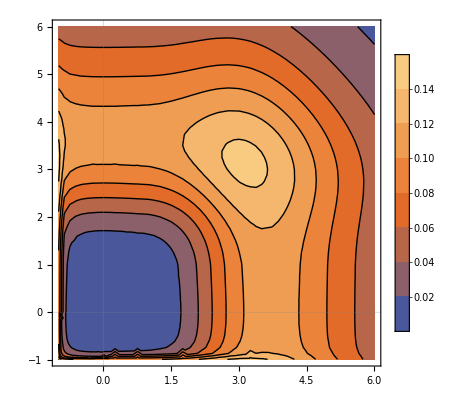

```mathematica
ContourPlot[en[kappalogrange[kx],kappalogrange[ky],0],{kx,-0.99,6},{ky,-0.99,6},PlotTheme->"Scientific", FrameTicksStyle->Directive[Black,15],PlotLegends->Automatic, AxesLabel->{MaTeX["\\kappa_{x}", Magnification->2], MaTeX["\\kappa_{y}", Magnification->2]}]
```

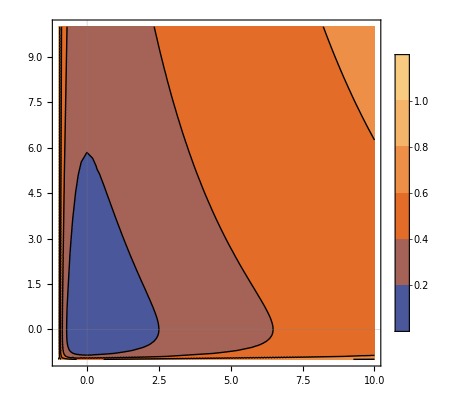

-Graphics-